# Fits to Brody distribution, and calculations for density of states

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
bins=Table[x,{x,0,5,0.2}];
bFit=Table[0.5*(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}];
Ewindowsize=30.0;
```

## Run1

```mathematica
rundata1=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-better/run1/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
60			100

LobattoPoints		NumChannels	Order
100			100		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
50.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.25d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff1-Ewindowsize<#<Ecutoff1-1.&;
curvestemp1=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-better/run1/AdiabaticCurves.dat"]];
Curves1=Table[Table[{curvestemp1[[1,i]],curvestemp1[[j,i]]},{i,1,Length[curvestemp1[[1]]]}],{j,2,Length[curvestemp1]}];
Evals1=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-better/run1/Eigenvals.dat"]];
Ecutoff1=Evals1[[4]]
Evals1=Sort[Drop[Evals1,1;;4]];
eValsBound1 = Sort[Select[Evals1,SampleRange]]
```

-117.568

{-147.377,-146.741,-146.695,-146.36,-145.412,-144.061,-143.88,-143.376,-142.743,-142.602,-142.245,-141.472,-140.733,-140.529,-140.352,-139.715,-139.052,-138.87,-138.534,-138.169,-137.767,-137.487,-136.293,-135.917,-135.643,-135.538,-135.118,-134.951,-134.368,-133.556,-133.225,-133.194,-132.447,-132.201,-131.795,-131.662,-131.399,-130.951,-130.735,-130.115,-129.61,-129.386,-128.799,-128.435,-128.259,-128.127,-128.044,-127.892,-127.55,-126.891,-126.794,-126.518,-126.473,-125.808,-125.69,-125.444,-125.299,-125.059,-124.841,-124.513,-124.148,-123.941,-123.773,-123.169,-122.658,-122.487,-122.146,-121.74,-121.432,-121.354,-121.238,-121.163,-121.023,-120.757,-120.674,-120.461,-120.209,-119.883,-119.782,-119.474,-119.301,-118.969,-118.93,-118.646}

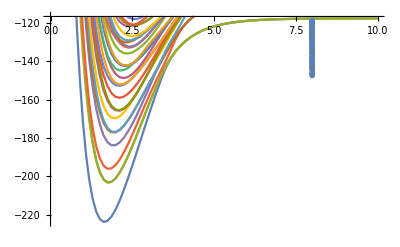

```mathematica
pcurves1=ListPlot[Curves1,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp1[[2]]],Ecutoff1+1}];
penergies1=ListPlot[Table[{8,eValsBound1[[i]]},{i,1,Length[eValsBound1]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves1,penergies1]
```

```mathematica
Es1=Table[eValsBound1[[i+1]]-eValsBound1[[i]],{i,1,Length[eValsBound1]-1}];
eTrim1= Select[Es1,#>0.0000001&];
avg1 = Mean[eTrim1];
eTrim1 = eTrim1/avg1;
(*Sort[eTrim1];*)
Length[Es1];
Length[eTrim1];
ρ1=1/avg1;
EspaceBin1=BinCounts[eTrim1,{bins}];
NormBrodyBinCs1=Table[EspaceBin1[[i]]/Total[EspaceBin1]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist1 = Table[{bFit[[i]],NormBrodyBinCs1[[i]]},{i,1,Length[bFit]}]
phist1=ListPlot[brodyPdist1,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars1 = FindFit[brodyPdist1,{PBrody[s,w],w>0,w<1},{w},s]
pfit1=Plot[PBrody[s,w/.pars1],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.240964},{0.3,0.662651},{0.5,0.843373},{0.7,0.722892},{0.9,0.722892},{1.1,0.481928},{1.3,0.120482},{1.5,0.180723},{1.7,0.240964},{1.9,0.361446},{2.1,0.120482},{2.3,0.120482},{2.5,0.},{2.7,0.060241},{2.9,0.},{3.1,0.},{3.3,0.},{3.5,0.060241},{3.7,0.},{3.9,0.060241},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.544551}

```mathematica
ρ1
```

2.88884

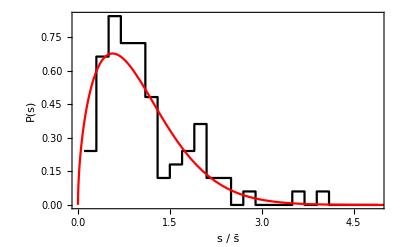

```mathematica
Show[phist1,pfit1,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run2

```mathematica
rundata2=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-better/run2/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
60			100

LobattoPoints		NumChannels	Order
100			100		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
50.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.25d0		0d0 		0.5d0

Left		Right		Bot		Top
0		1		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff2-Ewindowsize<#<Ecutoff2-1&
curvestemp2=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-better/run2/AdiabaticCurves.dat"]];
Curves2=Table[Table[{curvestemp2[[1,i]],curvestemp2[[j,i]]},{i,1,Length[curvestemp2[[1]]]}],{j,2,Length[curvestemp2]}];
Evals2=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-better/run2/Eigenvals.dat"]];
Ecutoff2=Evals2[[4]]
Evals2=Sort[Drop[Evals2,1;;4]];
eValsBound2 = Sort[Select[Evals2,SampleRange]]
```

Ecutoff2-Ewindowsize<#1<Ecutoff2-1&

-117.568

{-147.194,-147.049,-146.754,-146.507,-146.406,-146.117,-146.092,-145.273,-144.918,-144.43,-143.825,-143.729,-143.346,-142.673,-142.32,-142.117,-141.483,-140.631,-140.546,-140.437,-139.9,-139.613,-139.414,-138.869,-138.601,-138.582,-138.172,-138.063,-137.284,-137.014,-136.392,-135.819,-135.672,-135.518,-135.048,-134.816,-134.479,-134.038,-133.377,-133.222,-133.086,-132.752,-132.582,-132.526,-132.466,-131.954,-131.896,-131.688,-131.464,-131.092,-130.593,-130.09,-129.473,-129.162,-129.,-128.855,-128.331,-128.014,-127.891,-127.843,-127.526,-127.471,-126.972,-126.758,-126.509,-126.462,-126.355,-126.03,-125.598,-125.264,-125.104,-124.74,-124.365,-124.055,-123.592,-123.424,-123.112,-123.058,-122.876,-122.721,-122.608,-122.405,-122.265,-122.06,-121.738,-121.552,-121.468,-121.277,-120.927,-120.908,-120.555,-120.527,-120.228,-120.048,-119.907,-119.85,-119.582,-119.562,-119.344,-118.811,-118.67}

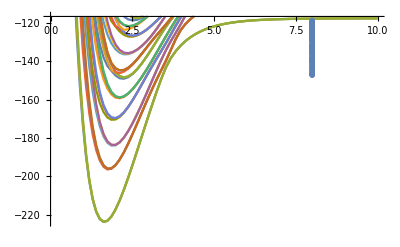

```mathematica
pcurves2=ListPlot[Curves2,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp2[[2]]],Ecutoff2+1}];
penergies2=ListPlot[Table[{8,eValsBound2[[i]]},{i,1,Length[eValsBound2]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves2,penergies2]
```

```mathematica
Es2=Table[eValsBound2[[i+1]]-eValsBound2[[i]],{i,1,Length[eValsBound2]-1}];
eTrim2 = Select[Es2,#>0.0000001&];
avg2 = Mean[eTrim2];
eTrim2 = eTrim2/avg2;
(*Sort[eTrim2];*)
Length[Es2];
Length[eTrim2];
ρ2=1/avg2;
EspaceBin2=BinCounts[eTrim2,{bins}];
NormBrodyBinCs2=Table[EspaceBin2[[i]]/Total[EspaceBin2]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist2 = Table[{bFit[[i]],NormBrodyBinCs2[[i]]},{i,1,Length[bFit]}]
phist2=ListPlot[brodyPdist2,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars2 = FindFit[brodyPdist2,{PBrody[s,w],w>0,w<1},{w},s]
pfit2=Plot[PBrody[s,w/.pars2],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.5},{0.3,0.55},{0.5,0.75},{0.7,0.6},{0.9,0.3},{1.1,0.7},{1.3,0.4},{1.5,0.15},{1.7,0.35},{1.9,0.2},{2.1,0.2},{2.3,0.15},{2.5,0.},{2.7,0.05},{2.9,0.1},{3.1,0.},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.388477}

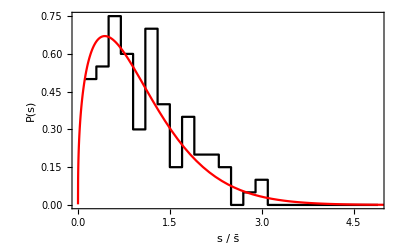

```mathematica
Show[phist2,pfit2,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run3

```mathematica
rundata3=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-better/run3/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
120			100

LobattoPoints		NumChannels	Order
100			160		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
50.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff3-Ewindowsize<#<Ecutoff3-1&
curvestemp3=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-better/run3/AdiabaticCurves.dat"]];
Curves3=Table[Table[{curvestemp3[[1,i]],curvestemp3[[j,i]]},{i,1,Length[curvestemp3[[1]]]}],{j,2,Length[curvestemp3]}];
Evals3=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run3/Eigenvals.dat"]];
Ecutoff3=Evals3[[4]]
Evals3=Sort[Drop[Evals3,1;;4]];
eValsBound3 = Sort[Select[Evals3,SampleRange]]
```

Ecutoff3-Ewindowsize<#1<Ecutoff3-1&

-117.567

{-147.377,-147.194,-147.049,-146.754,-146.741,-146.695,-146.507,-146.406,-146.36,-146.117,-146.092,-145.411,-145.273,-144.918,-144.43,-144.061,-143.88,-143.825,-143.729,-143.376,-143.346,-142.743,-142.673,-142.602,-142.32,-142.245,-142.117,-141.483,-141.472,-140.733,-140.631,-140.546,-140.529,-140.437,-140.352,-139.9,-139.715,-139.613,-139.414,-139.052,-138.87,-138.869,-138.601,-138.582,-138.534,-138.172,-138.169,-138.063,-137.767,-137.487,-137.284,-137.014,-136.392,-136.293,-135.917,-135.819,-135.672,-135.642,-135.538,-135.518,-135.118,-135.048,-134.951,-134.816,-134.479,-134.368,-134.038,-133.556,-133.377,-133.225,-133.222,-133.194,-133.086,-132.752,-132.582,-132.526,-132.466,-132.447,-132.201,-131.954,-131.896,-131.795,-131.688,-131.662,-131.464,-131.399,-131.092,-130.951,-130.735,-130.593,-130.115,-130.09,-129.61,-129.473,-129.386,-129.162,-129.,-128.855,-128.799,-128.435,-128.331,-128.259,-128.127,-128.044,-128.014,-127.892,-127.891,-127.843,-127.55,-127.526,-127.471,-126.972,-126.891,-126.794,-126.758,-126.518,-126.509,-126.473,-126.462,-126.355,-126.03,-125.808,-125.69,-125.598,-125.444,-125.299,-125.264,-125.104,-125.059,-124.841,-124.74,-124.513,-124.365,-124.148,-124.055,-123.941,-123.773,-123.592,-123.424,-123.169,-123.112,-123.058,-122.876,-122.721,-122.658,-122.608,-122.487,-122.405,-122.265,-122.146,-122.06,-121.74,-121.738,-121.552,-121.468,-121.432,-121.354,-121.277,-121.238,-121.163,-121.023,-120.927,-120.908,-120.757,-120.673,-120.554,-120.527,-120.461,-120.228,-120.209,-120.048,-119.907,-119.883,-119.85,-119.782,-119.582,-119.562,-119.473,-119.344,-119.301,-118.969,-118.93,-118.811,-118.67,-118.646}

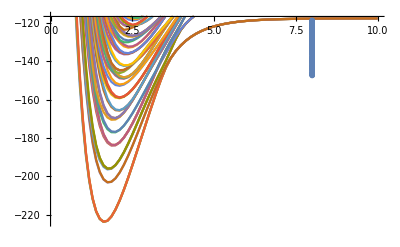

```mathematica
pcurves3=ListPlot[Curves3,Joined->True,PlotRange->{Min[curvestemp3[[2]]],Ecutoff3+1}];
penergies3=ListPlot[Table[{8,eValsBound3[[i]]},{i,1,Length[eValsBound3]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves3,penergies3]
```

```mathematica
Es3=Table[eValsBound3[[i+1]]-eValsBound3[[i]],{i,1,Length[eValsBound3]-1}];
eTrim3 = Select[Es3,#>0.0000001&];
avg3 = Mean[eTrim3];
eTrim3 = eTrim3/avg3;
Sort[eTrim3];
Length[Es3];
Length[eTrim3];
ρ3=1/avg3;
EspaceBin3=BinCounts[eTrim3,{bins}];
NormBrodyBinCs3=Table[EspaceBin3[[i]]/Total[EspaceBin3]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist3 = Table[{bFit[[i]],NormBrodyBinCs3[[i]]},{i,1,Length[bFit]}]
phist3=ListPlot[brodyPdist3,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->{Blue}];
pars3 = FindFit[brodyPdist3,{PBrody[s,w],w>0,w<1},{w},s]
pfit3=Plot[PBrody[s,w/.pars3],{s,0,5},PlotRange->All,PlotStyle->{Green}];
```

{{0.1,0.733696},{0.3,0.597826},{0.5,0.679348},{0.7,0.679348},{0.9,0.570652},{1.1,0.380435},{1.3,0.217391},{1.5,0.217391},{1.7,0.108696},{1.9,0.13587},{2.1,0.163043},{2.3,0.163043},{2.5,0.0543478},{2.7,0.},{2.9,0.0271739},{3.1,0.13587},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.0543478},{4.1,0.0271739},{4.3,0.0271739},{4.5,0.},{4.7,0.0271739},{4.9,0.}}

{w→0.17542}

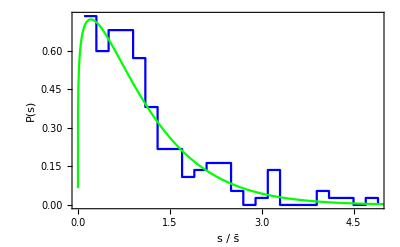

```mathematica
pall3=Show[phist3,pfit3,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

##### Analysis so far

Runs 1 and 2 have taken advantage of a possible symmetry by further reducing the coordinate space.  If my guess is right, then the density of states for run3 should be roughly twice that of run 1 and 2 since I expect both “even and odd” states about phi = π/4 to be present in run 3, but only even states in run1 and odd states in run2

```mathematica
ρ1
ρ2
ρ3
```

2.88884

3.50581

6.40417

```mathematica
ρ1+ρ2
```

6.39466

Further, I expect that if these states (even and odd) do not couple since the Hamiltonian is symmetric about ϕ=π/4, then overlaying these two distributions will result in a distribution similar to that of run3

```mathematica
eValsBoundCombined =Sort[ Flatten[{eValsBound1,eValsBound2}]]
EsCombined=Table[eValsBoundCombined[[i+1]]-eValsBoundCombined[[i]],{i,1,Length[eValsBoundCombined]-1}];
eTrimCombined = Select[EsCombined,#>0.0000001&];
avgCombined = Mean[eTrimCombined];
eTrimCombined = eTrimCombined/avgCombined;
(*Sort[eTrimCombined];*)
Length[eTrimCombined];
ρCombined=1/avgCombined;
EspaceBinCombined=BinCounts[eTrimCombined,{bins}];
NormBrodyBinCsCombined=Table[EspaceBinCombined[[i]]/Total[EspaceBinCombined]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdistCombined = Table[{bFit[[i]],NormBrodyBinCsCombined[[i]]},{i,1,Length[bFit]}]
phistCombined=ListPlot[brodyPdistCombined,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->{Black,Dashed}];
parsCombined = FindFit[brodyPdistCombined,{PBrody[s,w],w>0,w<1},{w},s]
pfitCombined=Plot[PBrody[s,w/.parsCombined],{s,0,5},PlotRange->All,PlotStyle->{Red,Dashed}];
```

{-147.377,-147.194,-147.049,-146.754,-146.741,-146.695,-146.507,-146.406,-146.36,-146.117,-146.092,-145.412,-145.273,-144.918,-144.43,-144.061,-143.88,-143.825,-143.729,-143.376,-143.346,-142.743,-142.673,-142.602,-142.32,-142.245,-142.117,-141.483,-141.472,-140.733,-140.631,-140.546,-140.529,-140.437,-140.352,-139.9,-139.715,-139.613,-139.414,-139.052,-138.87,-138.869,-138.601,-138.582,-138.534,-138.172,-138.169,-138.063,-137.767,-137.487,-137.284,-137.014,-136.392,-136.293,-135.917,-135.819,-135.672,-135.643,-135.538,-135.518,-135.118,-135.048,-134.951,-134.816,-134.479,-134.368,-134.038,-133.556,-133.377,-133.225,-133.222,-133.194,-133.086,-132.752,-132.582,-132.526,-132.466,-132.447,-132.201,-131.954,-131.896,-131.795,-131.688,-131.662,-131.464,-131.399,-131.092,-130.951,-130.735,-130.593,-130.115,-130.09,-129.61,-129.473,-129.386,-129.162,-129.,-128.855,-128.799,-128.435,-128.331,-128.259,-128.127,-128.044,-128.014,-127.892,-127.891,-127.843,-127.55,-127.526,-127.471,-126.972,-126.891,-126.794,-126.758,-126.518,-126.509,-126.473,-126.462,-126.355,-126.03,-125.808,-125.69,-125.598,-125.444,-125.299,-125.264,-125.104,-125.059,-124.841,-124.74,-124.513,-124.365,-124.148,-124.055,-123.941,-123.773,-123.592,-123.424,-123.169,-123.112,-123.058,-122.876,-122.721,-122.658,-122.608,-122.487,-122.405,-122.265,-122.146,-122.06,-121.74,-121.738,-121.552,-121.468,-121.432,-121.354,-121.277,-121.238,-121.163,-121.023,-120.927,-120.908,-120.757,-120.674,-120.555,-120.527,-120.461,-120.228,-120.209,-120.048,-119.907,-119.883,-119.85,-119.782,-119.582,-119.562,-119.474,-119.344,-119.301,-118.969,-118.93,-118.811,-118.67,-118.646}

{{0.1,0.733696},{0.3,0.597826},{0.5,0.679348},{0.7,0.679348},{0.9,0.570652},{1.1,0.380435},{1.3,0.217391},{1.5,0.217391},{1.7,0.108696},{1.9,0.13587},{2.1,0.163043},{2.3,0.163043},{2.5,0.0543478},{2.7,0.},{2.9,0.0271739},{3.1,0.13587},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.0543478},{4.1,0.0271739},{4.3,0.0271739},{4.5,0.},{4.7,0.0271739},{4.9,0.}}

{w→0.17542}

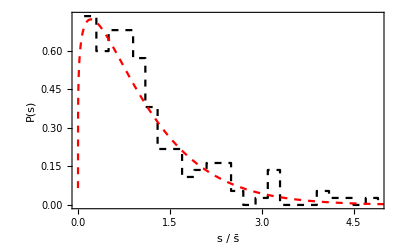

```mathematica
pcomb=Show[phistCombined,pfitCombined,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

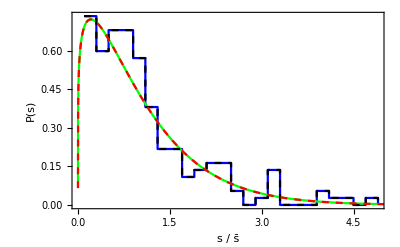

```mathematica
Show[pall3,pcomb]
```

## Run4

```mathematica
rundata4=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-better/run4/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
120			100

LobattoPoints		NumChannels	Order
100			160		5

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
50.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.5d0		1.5d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff4-Ewindowsize<#<Ecutoff4-1&
curvestemp4=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-better/run4/AdiabaticCurves.dat"]];
Curves4=Table[Table[{curvestemp4[[1,i]],curvestemp4[[j,i]]},{i,1,Length[curvestemp4[[1]]]}],{j,2,Length[curvestemp4]}];
Evals4=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-better/run4/Eigenvals.dat"]];
Ecutoff4=Evals4[[4]]
Evals4=Sort[Drop[Evals4,1;;4]];
eValsBound4 = Sort[Select[Evals4,SampleRange]]
```

Ecutoff4-Ewindowsize<#1<Ecutoff4-1&

-119.739

{-149.482,-149.163,-148.658,-148.509,-148.435,-148.392,-148.313,-148.179,-147.837,-147.669,-147.628,-147.309,-147.208,-146.937,-146.802,-146.773,-146.583,-146.397,-146.239,-145.623,-145.448,-145.355,-145.197,-144.946,-144.808,-144.565,-144.49,-144.347,-144.257,-144.198,-144.028,-143.674,-143.656,-143.477,-143.466,-143.194,-142.992,-142.89,-142.566,-142.262,-142.061,-142.008,-141.71,-141.573,-141.421,-141.227,-140.925,-140.768,-140.755,-140.607,-140.546,-140.445,-140.341,-140.112,-139.98,-139.896,-139.78,-139.323,-139.165,-138.943,-138.72,-138.468,-138.227,-138.195,-138.074,-138.025,-137.996,-137.81,-137.733,-137.627,-137.536,-137.503,-137.347,-137.104,-137.021,-136.821,-136.748,-136.661,-136.604,-136.427,-136.256,-136.204,-135.61,-135.553,-135.472,-135.314,-135.171,-135.131,-135.044,-134.967,-134.738,-134.575,-134.488,-134.414,-134.343,-134.236,-134.154,-134.044,-133.924,-133.746,-133.705,-133.48,-133.327,-133.034,-132.629,-132.589,-132.487,-132.449,-132.406,-132.319,-132.261,-131.981,-131.957,-131.698,-131.611,-131.517,-131.377,-131.251,-131.19,-131.083,-131.009,-130.984,-130.904,-130.696,-130.587,-130.526,-130.376,-130.332,-130.04,-129.944,-129.796,-129.7,-129.532,-129.383,-129.291,-129.231,-129.162,-129.039,-128.986,-128.902,-128.692,-128.587,-128.521,-128.412,-128.311,-128.249,-128.033,-127.839,-127.782,-127.746,-127.671,-127.64,-127.579,-127.539,-127.489,-127.389,-127.308,-127.092,-126.974,-126.756,-126.668,-126.537,-126.431,-126.386,-126.329,-126.159,-126.115,-126.056,-125.991,-125.891,-125.698,-125.445,-125.265,-125.114,-125.007,-124.973,-124.941,-124.78,-124.719,-124.692,-124.6,-124.556,-124.473,-124.423,-124.382,-124.365,-124.27,-124.237,-124.081,-124.006,-123.872,-123.824,-123.811,-123.716,-123.69,-123.472,-123.413,-123.381,-123.244,-123.199,-122.941,-122.931,-122.734,-122.661,-122.584,-122.509,-122.344,-122.319,-122.246,-122.197,-122.076,-121.998,-121.875,-121.827,-121.71,-121.659,-121.619,-121.51,-121.491,-121.417,-121.391,-121.28,-121.25,-121.16,-121.131,-121.071,-120.992,-120.92,-120.862,-120.774}

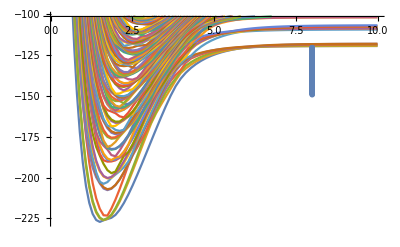

```mathematica
pcurves4=ListPlot[Curves4,Joined->True,PlotRange->{Min[curvestemp4[[2]]],Ecutoff4+18}];
penergies4=ListPlot[Table[{8,eValsBound4[[i]]},{i,1,Length[eValsBound4]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves4,penergies4]
```

```mathematica
Es4=Table[eValsBound4[[i+1]]-eValsBound4[[i]],{i,1,Length[eValsBound4]-1}];
eTrim4 = Select[Es4,#>0.0000001&];
avg4 = Mean[eTrim4];
eTrim4 = eTrim4/avg4;
Sort[eTrim4];
Length[Es4];
Length[eTrim4];
ρ4=1/avg4;
EspaceBin4=BinCounts[eTrim4,{bins}];
NormBrodyBinCs4=Table[EspaceBin4[[i]]/Total[EspaceBin4]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist4 = Table[{bFit[[i]],NormBrodyBinCs4[[i]]},{i,1,Length[bFit]}]
phist4=ListPlot[brodyPdist4,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars4 = FindFit[brodyPdist4,{PBrody[s,w],w>0,w<1},{w},s]
pfit4=Plot[PBrody[s,w/.pars4],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.196507},{0.3,0.786026},{0.5,0.829694},{0.7,0.720524},{0.9,0.567686},{1.1,0.371179},{1.3,0.414847},{1.5,0.262009},{1.7,0.240175},{1.9,0.131004},{2.1,0.131004},{2.3,0.0873362},{2.5,0.10917},{2.7,0.0218341},{2.9,0.0218341},{3.1,0.},{3.3,0.0218341},{3.5,0.},{3.7,0.0218341},{3.9,0.},{4.1,0.0218341},{4.3,0.},{4.5,0.},{4.7,0.0218341},{4.9,0.0218341}}

{w→0.530213}

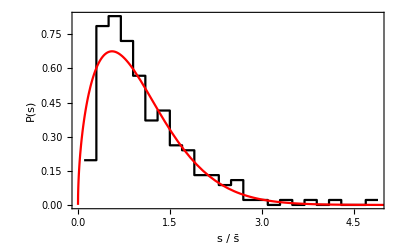

```mathematica
pall4=Show[phist4,pfit4,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

```mathematica
ρ4
```

7.9768

## We need to more closely examine the identical particle symmetries and any other symmetries in the Hamiltonian in order to understand these spectra.

We defined the Jacobi coordinates in the H-tree above so that:

(y⃗)^(12)=S_12 x⃗

where:

1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))

To keep things as general as possible I’ll assume for now that only particle 1 is of different mass and let m_2=m_3=m_4=m, and m_1=γ m  Then

μ_12=(γ m m)/(γ m+m)=mγ/(1+γ) ⟶ m/2

μ_34=m/2

μ_(12,34)=((γ m+m)(2m))/(3m+γ m)=2m(1+γ)/(3+γ)⟶ m

μ=((γ m m m m)/(γ m+3m))^(1/3)=(m(γ/(3+γ)))^(1/3) ⟶ (m/2^(2/3))

So for the equal-mass case:

2^(1/3)/(√m)(√(m/2) | -√(m/2) | 0 | 0
0 | 0 | √(m/2) | -√(m/2)
(√m)/2 | (√m)/2 | -(√m)/2 | -(√m)/2
m/(√(4m)) | m/(√(4m)) | m/(√(4m)) | m/(√(4m)))=2^(1/3)(√(1/2) | -√(1/2) | 0 | 0
0 | 0 | √(1/2) | -√(1/2)
1/2 | 1/2 | -1/2 | -1/2
1/2 | 1/2 | 1/2 | 1/2)

and

x⃗=S_12^-1(y⃗)^(12)

Then

(y⃗)^(13)=S_13 x⃗=S_13 S_12^-1(y⃗)^(12)

Now note that we could use the same matrix S_12 to construct (y⃗)^(13) if the matrix were to act on a column vector (x_1
x_3
x_2
x_4)  instead of the usual vector x⃗= (x_1
x_2
x_3
x_4).  We can then say:

(x_1
x_3
x_2
x_4) =(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)(x_1
x_2
x_3
x_4)=P_23 x⃗

Hence:

S_13=S_12 P_23

and

(y⃗)^(13)=S_13 x⃗=S_13 S_12^-1(y⃗)^(12)=S_12 P_23 S_12^-1(y⃗)^(12)

Similarly,

(y⃗)^(14)=S_14 x⃗=S_14 S_12^-1(y⃗)^(12)=S_12 P_24 S_12^-1(y⃗)^(12)

where

P_24=(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
S12=2^(1/3)({{√(1/2), -√(1/2), 0, 0}, {0, 0, √(1/2), -√(1/2)}, {1/2, 1/2, -1/2, -1/2}, {1/2, 1/2, 1/2, 1/2}});
```

```mathematica
P24=({{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}});P23=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});P34=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});P14=({{0, 0, 0, 1}, {0, 1, 0, 0}, {0, 0, 1, 0}, {1, 0, 0, 0}});P13=({{0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}});P12=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
𝒫12=Simplify[S12.P12.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫12]
```

(-1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
𝒫34=Simplify[S12.P34.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫34]
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

```mathematica
𝒫14=Simplify[S12.P14.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫14]
```

(1/2 | -1/2 | -1/(√2)
-1/2 | 1/2 | -1/(√2)
-1/(√2) | -1/(√2) | 0)

```mathematica
𝒫13=Simplify[S12.P13.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫13]
```

(1/2 | 1/2 | -1/(√2)
1/2 | 1/2 | 1/(√2)
-1/(√2) | 1/(√2) | 0)

```mathematica
𝒫23=Simplify[S12.P23.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫23]
```

(1/2 | -1/2 | 1/(√2)
-1/2 | 1/2 | 1/(√2)
1/(√2) | 1/(√2) | 0)

```mathematica
𝒫24=Simplify[S12.P24.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫24]
```

(1/2 | 1/2 | 1/(√2)
1/2 | 1/2 | -1/(√2)
1/(√2) | -1/(√2) | 0)

```mathematica
TraditionalForm[FullSimplify[𝒫23.𝒫14]]
```

(0 | -1 | 0
-1 | 0 | 0
0 | 0 | -1)

```mathematica
TraditionalForm[FullSimplify[𝒫24.𝒫13]]
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | -1)

```mathematica
TraditionalForm[FullSimplify[𝒫23.𝒫14.𝒫24.𝒫13]]
```

(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

X_cm=(m_1 x_1+m_2 x_2+m_3 x_3+m_4 x_4)/(m_1+m_2+m_3+m_4)

ρ_1^(12)=x_1-x_2

ρ_2^(12)=x_3-x_4

ρ_3^(12)=(m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4)

and mass-scaled Jacobi coordinates as:

y_1^(12)=√(μ_12/μ)(x_1-x_2)

y_2^(12)=√(μ_34/μ)(x_3-x_4)

y_3^(12)=√((μ_(12,34))/μ)((m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4))

y_4^(12)=√(M/μ)X_cm

The convention here is that the superscript (12) indicates this coordinate system is convenient for treating the interaction between particles 1 and 2.  In matrix notation:

(y_1^(12)
y_2^(12)
y_3^(12)
y_4^(12))=1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))(x_1
x_2
x_3
x_4)

Now we define the hyperspherical coordinates as:

y_1^(12)=cos θ_12

y_2^(12)=sin θ_12 cos ϕ_12

y_3^(12)=sin θ_12 sin ϕ_12

```mathematica
Clear[μ4]
```

```mathematica
μ4=(μ12 μ34 μ1234)^(1/3)/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}
```

((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/3)

```mathematica
A=1/(√μ4)({{√μ12, -√μ12, 0, 0}, {0, 0, √μ34, -√μ34}, {(√μ1234 m1)/(m1+m2), (√μ1234 m2)/(m1+m2), -(√μ1234 m3)/(m3+m4), -(√μ1234 m4)/(m3+m4)}, {m1/(√M), m2/(√M), m3/(√M), m4/(√M)}})/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}//FullSimplify
```

{{(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),0,0},{0,0,(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)},{(m1 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),(m2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m3 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m4 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6))},{m1/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m2/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m3/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m4/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4))}}

Let’s just treat the equal mass case here...

```mathematica
({{x1}, {x2}, {x3}, {x4}})=FullSimplify[Inverse[A].({{x}, {y}, {z}, {XCM}})/.{m1->m,m2->m,m3->β m,m4->β m}];
```

```mathematica
Clear[R]
```

```mathematica
x12=Simplify[x1-x2];FullSimplify[x12,{m>0,β>0}]
x12hyp=Simplify[x12,m>0]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x12hyp,m>0]
```

(2^(1/3) x β^(1/3))/(1+β)^(1/6)

2^(1/3) R (β^2/(1+β))^(1/6) Cos[ϕ] Sin[θ]

```mathematica
x13=FullSimplify[x1-x3,{m>0,β>0}]
x13hyp=Simplify[x13]/.{x->R Sin[θ]Cos[ϕ],y-> R Sin[θ]Sin[ϕ],z-> R Cos[θ]};FullSimplify[x13hyp,{m>0,β>0}]
```

(√m x β-y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (√m β Cos[ϕ]-√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x14=FullSimplify[x1-x4,{m>0,β>0}]
x14hyp=Simplify[x14]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x14hyp,{m>0,β>0}]
```

(√m x β+y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x23=Simplify[x2-x3,{m>0,β>0}]
x23hyp=Simplify[x23]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x23hyp,{m>0,β>0}]
```

-(√m x β+y √(m β)-z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]-Sin[θ] (√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x24=Simplify[x2-x4,{m>0,β>0}]
x24hyp=Simplify[x24]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x24hyp,{m>0,β>0}]
```

(-√m x β+y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (-√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x34=Simplify[x3-x4,{m>0,β>0}]
x34hyp=Simplify[x3-x4,{m>0,β>0}]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x34hyp,{m>0,β>0}]
```

(2^(1/3) y)/(β (1+β))^(1/6)

(2^(1/3) R Sin[θ] Sin[ϕ])/(β (1+β))^(1/6)

```mathematica
Clear[unequalmassxij]
```

```mathematica
unequalmassxij[R_,β_]=FullSimplify[{x12hyp,x13hyp,x14hyp,x23hyp,x24hyp,x34hyp}/.{m->1,θ->t π,ϕ->f π}]
```

{2^(1/3) R (β^2/(1+β))^(1/6) Cos[f π] Sin[π t],(R (√(β (1+β)) Cos[π t]+β Cos[f π] Sin[π t]-√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]+β Cos[f π] Sin[π t]+√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]-√β (√β Cos[f π]+Sin[f π]) Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]-β Cos[f π] Sin[π t]+√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(2^(1/3) R Sin[f π] Sin[π t])/((β+β^2)^(1/6))}

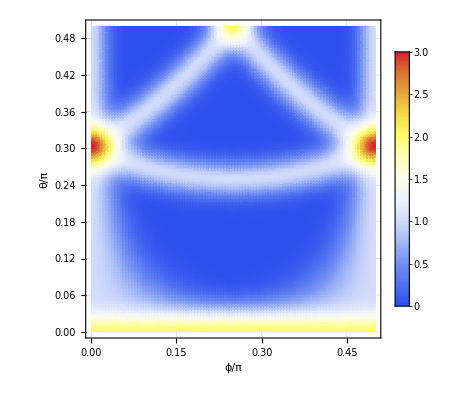

```mathematica
beta=1.0;DensityPlot[Sum[Exp[-(unequalmassxij[10,beta][[i]])^2],{i,1,6}]==0,{f,0.0,.5},{t,0,0.5},GridLines->Automatic,ColorFunction->"TemperatureMap",FrameLabel->{"ϕ/π","θ/π"},PlotPoints->100,PlotLegends->Automatic]
```

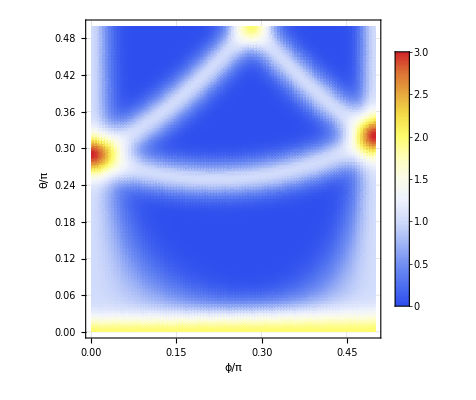

```mathematica
beta=1.5;DensityPlot[Sum[Exp[-(unequalmassxij[10,beta][[i]])^2]/.β->beta,{i,1,6}]==0,{f,0.0,.5},{t,0,0.5},GridLines->Automatic,ColorFunction->"TemperatureMap",FrameLabel->{"ϕ/π","θ/π"},PlotPoints->100,PlotLegends->Automatic]
```

```mathematica
unequalmassxij[[1]]==0
```

5 2^(1/3) (β^2/(1+β))^(1/6) Cos[f π] Sin[π t]==0

```mathematica
c12[β_]:=ContourPlot[Evaluate[unequalmassxij[[1]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Black,FrameLabel->{"ϕ/π","θ/π"}]
c13[β_]:=ContourPlot[Evaluate[unequalmassxij[[2]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Red,FrameLabel->{"ϕ/π","θ/π"}];
c14[β_]:=ContourPlot[Evaluate[unequalmassxij[[3]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Blue,FrameLabel->{"ϕ/π","θ/π"}];
c23[β_]:=ContourPlot[Evaluate[unequalmassxij[[4]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Green,FrameLabel->{"ϕ/π","θ/π"}];
c24[β_]:=ContourPlot[Evaluate[unequalmassxij[[5]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Orange,FrameLabel->{"ϕ/π","θ/π"}];
c34[β_]:=ContourPlot[Evaluate[unequalmassxij[[6]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Yellow,FrameLabel->{"ϕ/π","θ/π"}];
```

```mathematica
c12[1.0]
```

-Graphics-

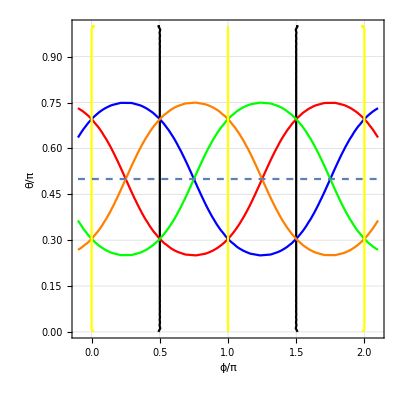

```mathematica
pall=Show[{c12,c13,c14,c23,c24,c34},Plot[0.5,{x,-.1,2.1},PlotStyle->Dashed]]
```

```mathematica
cptable=Table[ContourPlot[Evaluate[unequalmassxij[[i]]==0/.{R->1,α->1}],{f,0,.5},{t,0,.5},GridLines->Automatic,ContourStyle->Black],{i,1,6}];
```

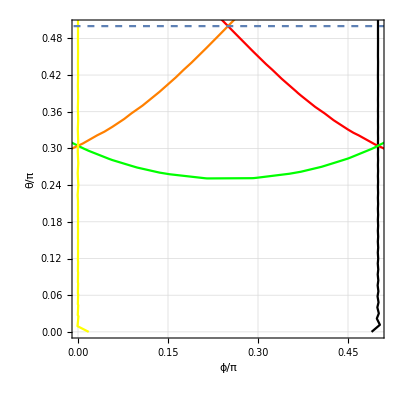

```mathematica
Show[pall,PlotRange->{{0,0.5},{0,0.5}}]
```

### Construct a simpler model with numerical solution

Consider a 3D Hamiltonian of the form

H=ℏ^2/(2μ)∇^2 + 1/2μ r^2+k_xy x y+k_xz x z+k_yz y z

H=ℏ^2/(2μ)∇^2 + 1/2μ r^2+k_xy x y+k_xz x z+k_yz y z

Sakurai, Modern QM page 217 (translated to my preferred notation)

∫ⅆΩ Y_l^(m*)(Ω)Y_l_1^m_1(Ω)Y_l_2^m_2(Ω)=√(((2 l_1+1)(2 l_2+1))/(4π (2l+1)))l_1 0, l_2 0(l_1 l_2) l 0l_1 m_1 l_2 m_2 (l_1 l_2) l m

```mathematica
ME3[l_,m_,l1_,m1_,l2_,m2_]:=√(((2l1+1)(2l2+1))/(4π (2l+1)))ClebschGordan[{l1,0},{l2,0},{l,0}]ClebschGordan[{l1,m1},{l2,m2},{l,m}]
```

So if we need matrix elements of the form:

∫ⅆΩ Y_l^(m*)(Ω)Y_2^m_1(Ω)Y_l_2^m_2(Ω)=√((5(2 l_2+1))/(4π (2l+1)))2,0, l_2,0(l_1 l_2) l 02 m_1 l_2 m_2 (2 l_2) l m

```mathematica
Simplify[ME3[l,m,2,m1,l2,m2]]
```

Piecewise[{{1/(2 (2+l-l2) (l-l2)!)(-1)^(-3 l2+m) (1+2 l) (l^3+l^2 (1+l2)-l (2+2 l2+l2^2)-l2 (2+3 l2+l2^2)) √((5+10 l2)/(π+2 l π)) √(((2+l-l2)!)/((-1+l+l2) (l+l2) (1+l+l2) (2+l+l2) (3+l+l2) (2-l+l2)!)) ThreeJSymbol[{2,m1},{l2,m2},{l,-m}], l∈ℤ&&l2∈ℤ&&l≥0&&l2≥0&&l+l2≥2&&l2≤2+l&&l≤2+l2}, {0, True}}]

Now, since we know

x y = r^2 √(30/π)i (Y_2^-2-Y_2^2)

```mathematica
MExy[R_,l_,m_,l2_,m2_]:=R^2 ⅈ √(30/π)(ME3[l,m,2,-2,l2,m2]-ME3[l,m,2,2,l2,m2])
```

Now the issue is if we want to apply this model to test the two-component 4-fermion problem in 1D, then we need to know how to construct systematically the symmetrized 4-fermion harmonics.  We can specify the subset of harmonics by the boundary conditions implied by identical particle symmetry:

ψ(ϕ=0,θ)=ψ(ϕ=π/2,θ)=0

requires a superposition ψ~Y_l^m-(-1)^m Y_l^-m

```mathematica
Integrate[SphericalHarmonicY[lb,mb,θ,ϕ]SphericalHarmonicY[k,q,θ,ϕ]SphericalHarmonicY[lk,mk,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

∫_0^π ∫_0^(2 π) Sin[θ] SphericalHarmonicY[k,q,θ,ϕ] SphericalHarmonicY[lb,mb,θ,ϕ] SphericalHarmonicY[lk,mk,θ,ϕ]ⅆϕⅆθ